## Bh and NoBh Region for (α and Q space time parameters)

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

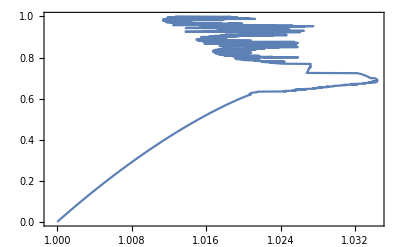

-0.446205

```mathematica
f[r_,Q_,a_] := 1-2/r+Q^2/r^2-(a *Q^4)/(20 *r^6)
aa=Table[a,{a,0.,1,0.001}];
QQ = Table[Q/.FindRoot[{(f[r,Q,a]/.{a->aa[[i]]})==0,D[(f[r,Q,a]/.{a->aa[[i]]}),r]==0},{{r,1},{Q,1}}],{i,1,Length[aa]}];
QQaa = Table[{QQ[[i]],aa[[i]]},{i,1,Length[aa]}];
Qqaa = Table[{aa[[i]],QQ[[i]]},{i,1,Length[aa]}];
ListLinePlot[QQaa,Frame->True]
ListLinePlot[Qqaa,Frame->True];
a/.FindRoot[{(f[r,Q,a]/.{Q->0.99})==0,D[(f[r,Q,a]/.{Q-> 0.99}),r]==0},{{r,1},{a,0.445}}]
```

## lapse function

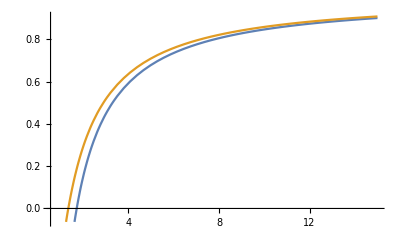

```mathematica
g[r_,Q_,a_,α_] = 1-2/r+Q^2/r^2-(a*Q^4)/(20 *r^6)+α/r Log[r/Abs[α]];
Plot[{g[r,0.,-1,0.1],g[r,0.7,-0.5,0.12]},{r,0.56,15}]
```

## Angular momentum and energy

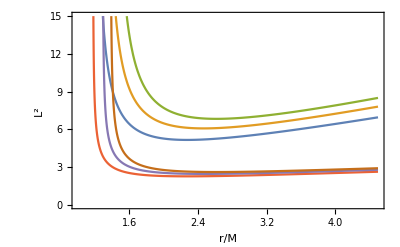

```mathematica
Ene = (-g[r,Q,a,α])/Sqrt[-g[r,Q,a,α] - r^2  *D[g[r,Q,a,α],r]/(2r)];//Simplify
L [r_,Q_,a_,α_]= (r^2 *Sqrt[(-D[g[r,Q,a,α],r])/(2 *r)])/Sqrt[-g[r,Q,a,α] - r^2  *D[g[r,Q,a,α],r]/(2r)];//Simplify

Plot[{L[r,0.3,0.5,-0.1]*L[r,0.3,0.5,-0.1],L[r,0.3,0.5,-0.2]*L[r,0.3,0.5,-0.2],L[r,0.3,0.5,-0.3]*L[r,0.3,0.5,-0.3],L[r,0.3,0.5,-0.1],L[r,0.3,0.5,-0.2],L[r,0.3,0.5,-0.3]},{r,1,4.5},Frame->True,FrameLabel->{"r/M ","L^2"},PlotRange->{{1,4.5},{0,15}}]
```

## Effective Potential

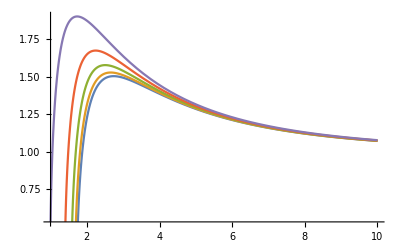

```mathematica
Vef[r_,Q_,a_,α_] := Sqrt[g[r,Q,a,α] + (36* g[r,Q,a,α])/r^2]
Plot[{Vef[r,0.,-1,0.1],Vef[r,0.3,-0.5,0.1],Vef[r,0.5,0.5,0.1],Vef[r,0.7,0.5,0.1],Vef[r,0.9,1,0.1]},{r,1.,10}]
```

## ISCO radius

```mathematica
y[x_]=x;
```